```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.2.2/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.2.2/~$Книга1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.2.2/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset 1

```mathematica
dataset1=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"m"->(#m &),"zm"-> (Around[#zm, #dzm] &)|>]
```

Dataset[<>]

```mathematica
line1 =LinearModelFit[(Normal@dataset1[All,{"m","zm"}/*Values]),{1,x},x]
```

FittedModel[-0.00021978+0.0472308 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.00021978 | 0.00107838 | -0.203806 | 0.841921
x | 0.0472308 | 0.000227342 | 207.752 | 1.04038×10^-22

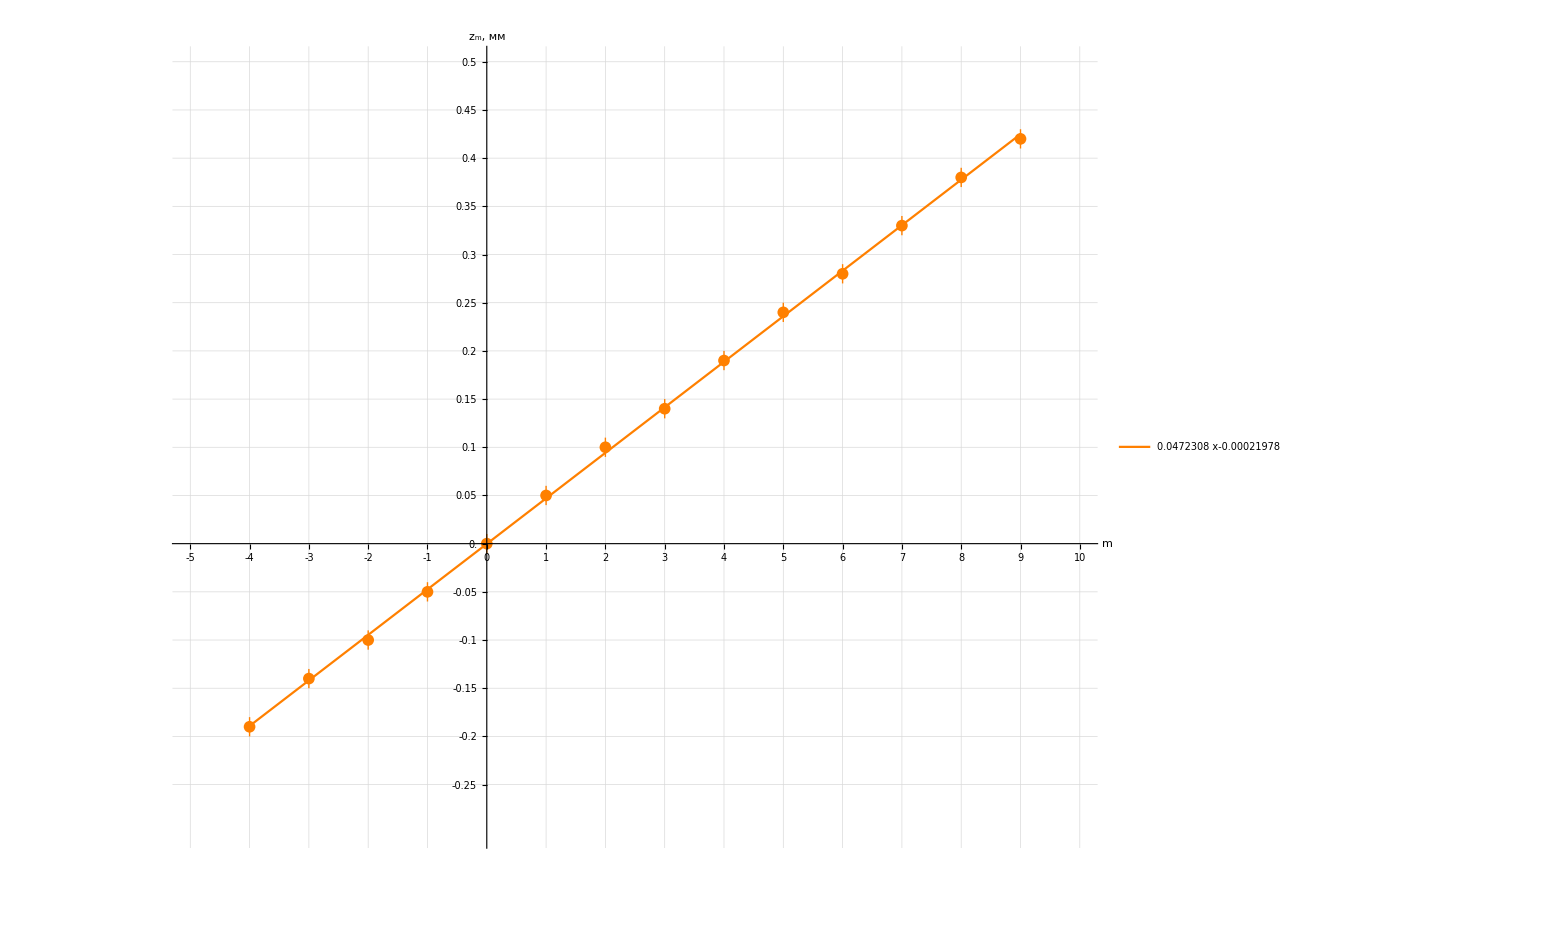

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
Ticks-> {Range[-5,10,1],Range[-0.25,0.5,0.05]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["m",Large],Style["z_m, мм",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{-5,10},{-0.3,0.5}},

GridLines->{Range[-5,10,0.25], Range[-10,50,0.02]},
LabelStyle->Black,
PlotStyle->Orange
],
Plot[
{line1@x},
{x,-4, 9},
PlotLegends->Placed[
LineLegend[
{Normal@line1, line1["ParameterTable"]},
LabelStyle->20
],
{Scaled[0.5],Scaled[0.75]}
],
PlotStyle->Orange
]
]
```

## Dataset2

```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.2.2/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.2.2/~$Книга1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.2.2/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
dataset2=makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"dP"->(Around[#DP,#dDp] &),"dz"-> (Around[#dz, #ddz] &)|>]
```

Dataset[<>]

```mathematica
line2 =LinearModelFit[(Normal@dataset2[All,{"DP","dz"}/*Values]),{1,x},x]
```

FittedModel[-3.41607×10^-17+0.0002 x]

```mathematica
line2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -3.41607×10^-17 | 3.23217×10^-17 | -1.0569 | 0.313218
x | 0.0002 | 8.63835×10^-20 | 2.31526×10^15 | 1.2259×10^-164

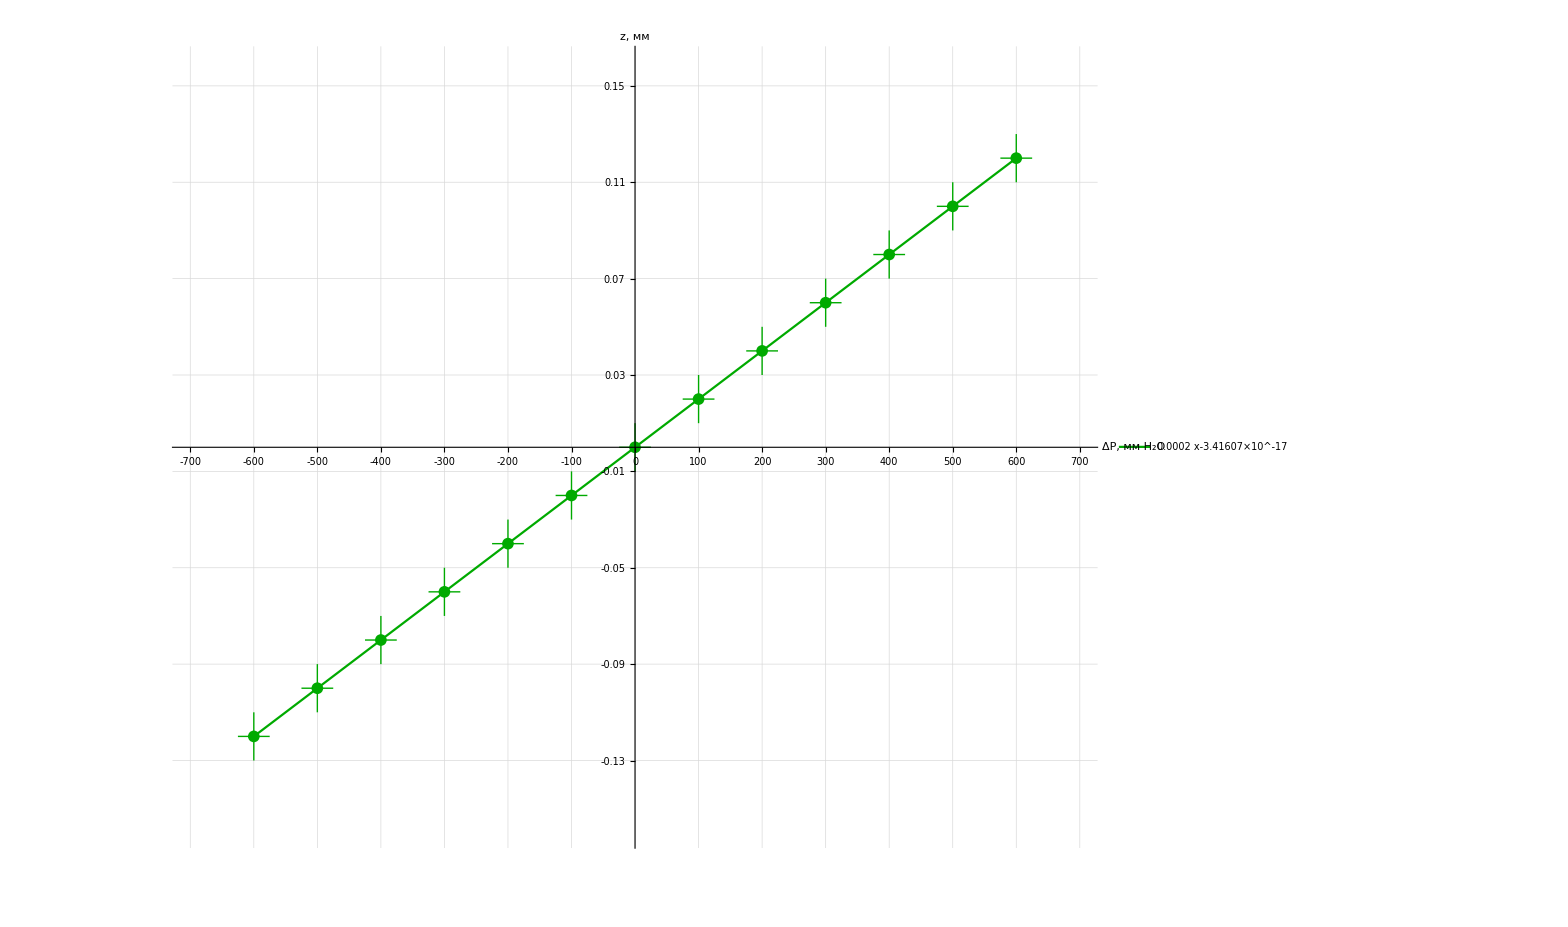

```mathematica
Show[
ListPlot[
{dataset2WithErrs},

PlotRange->{{-700,700},{-0.16,0.16}},

Ticks-> {Range[-700,700,50],Range[-0.25,0.5,0.02]},

GridLines->{Range[-1000,1000,25], Range[-1000,1000,0.01]},

AxesLabel->{Style["ΔP, \n мм H_2O",Large],Style["z, мм",Large]},

TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
LabelStyle->Black,
PlotStyle->Darker@Green
],
Plot[
{line2@x},
{x,-600, 600},
PlotLegends->Placed[
LineLegend[
{Normal@line2, line2["ParameterTable"]},
LabelStyle->20
],
{Scaled[0.7],Scaled[0.83]}
],
PlotStyle->Darker@Green
]
]
```